# First Solution

```mathematica
ClearAll["Global`*"]
equation = (x^2-1)^2y''[x]+((2-2L)x^3+(-3+2L)x+1/x)y'[x]+(L(L-1)(x^2-1)+d^2(1-1/x^2))y[x]==0;
sol[x_]=DSolveValue[{equation,y[0]==0,y[1]==1},y,x][x]/.{0^d->0}
```

(x^d Hypergeometric2F1[d/2-L/2,1/2+d/2-L/2,1+d,x^2])/Hypergeometric2F1[d/2-L/2,1/2+d/2-L/2,1+d,1]

```mathematica
N[sol[x]/.{L->180,d->0}/.{x->0}]
```

1.55279×10^-53

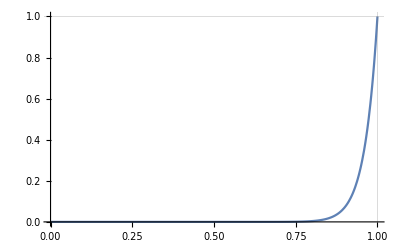

```mathematica
Plot[sol[x]/.{L->40,d->21},{x,0,1},PlotRange->{{0,1},{0,1}},GridLines->{{1},{1}}]
```

```mathematica
l = 40
k = 21
```

40

21

```mathematica
pa = Table[SeriesCoefficient[sol[x]/.{L->l,d->k},{x,0,n}],{n,0,l}];
```

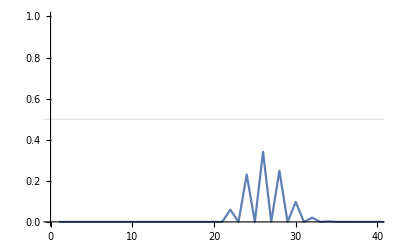

```mathematica
ListLinePlot[pa,PlotRange->{{0,l},{0,1}},GridLines->{{},{0.5}}]
```

```mathematica
parray = Table[SeriesCoefficient[sol[x]/.{L->40,d->21},{x,0,n}],{n,0,40}];
```

```mathematica
p30_13
```

## Exporting Results

```mathematica
SetDirectory["/home/sven/Desktop"]
```

/home/sven/Desktop

```mathematica
Export["pl40d21.txt",N[parray]]
```

pl40d21.txt

```mathematica
Export["p180.txt",p180]
```

p180.txt

```mathematica
Export["p760_N.txt",N[p760]]
```

p760_N.txt

```mathematica
Export["p180_N.txt",N[p180]]
```

p180_N.txt

```mathematica
p3120 = Table[SeriesCoefficient[sol[x]/.{L->3120,d->0},{x,0,n}],{n,0,3120}];
```

```mathematica
ListLinePlot[p3120,PlotRange->{{1475,1650},{0,0.04}},GridLines->{{},{0.03}}]
```

General::munfl: 6.054568002116552×10^-938 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.472967412690919×10^-931 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 8.947177830165612×10^-926 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

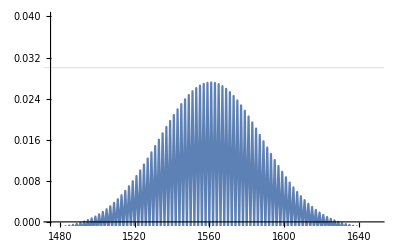

```mathematica
Export["p3120_N.txt",N[p3120,10]]
```

p3120_N.txt

```mathematica
Manipulate[ListLinePlot[Table[SeriesCoefficient[sol[x]/.{L->l,d->k},{x,0,n}],{n,0,l}],PlotRange->{{0,l},{0,1}},GridLines->{{},{0.5}}],{l,0,1000,1},{k,0,l,1}]
```

```mathematica
N[D[sol[x]/.{L->180,d->0},x]/.{x->1}]
```

89.7493

```mathematica
N[D[sol[x],{x,90}]/.{L->180,d->0}/.{x->0}]
```

1.76101×10^137